## AirFoils

http : // airfoiltools.com/airfoil/naca4digit

Domains:

0≤x≤1

Max Camber: 0<M<0.095

Max Camber Position: 0<P<0.9

Thickness: 0.01<T<0.40

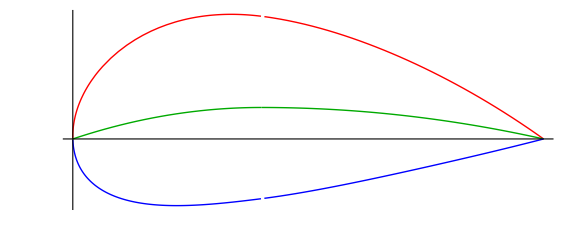

```mathematica
Clear[M,p,yc,T,a0,a1,a2,a3,a4,yt,yc,lower,upper,camber]

(* camber *)
M=0.02; (* M is the maximum camber divided by 100 *)
p=0.4; (* p is the position of the maximum camber divided by 4 *)

yc[x_]:=Piecewise[{{M/p^2(2*p*x-x^2),0≤x<p},{M/(1-p)^2(1-2p+2*p*x-x^2),p≤x≤1}}]

(* thickness distribution *)
T=0.12; (* *)

a0=0.2969;
a1=-0.126;
a2=-0.3516;
a3=0.2843;
a4=-0.1015; (* open trainling edge*)
a4=-0.1036; (* closed trainling edge*)
yt[x_]:=T/0.2(a0 √x+a1*x+a2*x^2+a3*x^3+a4*x^4)

θ[x_]:=ArcTan[yc'[x]];

camber[x_]:={x,yc[x]} (* note this could be defined as an explicit function *)
upper[x_]:={x- yt[x]*Sin[θ[x]],yc[x]+yt[x]*Cos[θ[x]]}
lower[x_]:={x + yt[x]*Sin[θ[x]],yc[x]-yt[x]*Cos[θ[x]]}

ParametricPlot[{upper[x],camber[x],lower[x]},{x,0,1},ImageSize->Large,PlotStyle->{{Red,Thick},{Darker[Green],Thick},{Blue,Thick}},PlotPoints->60,Ticks->False]
```

Notice the slight discontinuity at the point p=0.4, which is where the piecewise function is defined.

Typically when integrating a parametric function to determine an area we would use the following:

x=x(t), y=y(t)

Area=∫_0^1 yⅆx=∫_0^1 y(t)ⅆx/ⅆt ⅆt=∫_0^1 y(t)x'(t)ⅆt.

Mathematica has some issues doing the integral exactly (which we don’t need anyway).

No issues doing the integral numerically (integrate to the camber to check things are working correctly):

```mathematica
camber'[x]⟦1⟧
```

1

```mathematica
NIntegrate[upper[x]⟦2⟧upper'[x]⟦1⟧-camber[x]⟦2⟧camber'[x]⟦1⟧,{x,0,1}]
```

0.0410747

```mathematica
NIntegrate[camber[x]⟦2⟧camber'[x]⟦1⟧-lower[x]⟦2⟧lower'[x]⟦1⟧,{x,0,1}]
```

0.0407028

```mathematica
NIntegrate[upper[x]⟦2⟧upper'[x]⟦1⟧-lower[x]⟦2⟧lower'[x]⟦1⟧,{x,0,1}]
```

0.0817774

## Table of x coordinates of upper, camber, lower as a function of the parameter x (shows these are not the same!)

```mathematica
Table[{upper[x]⟦1⟧,camber[x]⟦1⟧,lower[x]⟦1⟧},{x,0.01,1,0.02}]//TableForm
```

0.00834672 | 0.01 | 0.0116533
0.027384 | 0.03 | 0.032616
0.0469015 | 0.05 | 0.0530985
0.0666402 | 0.07 | 0.0733598
0.0865191 | 0.09 | 0.0934809
0.106498 | 0.11 | 0.113502
0.126552 | 0.13 | 0.133448
0.146666 | 0.15 | 0.153334
0.166826 | 0.17 | 0.173174
0.187024 | 0.19 | 0.192976
0.207252 | 0.21 | 0.212748
0.227504 | 0.23 | 0.232496
0.247774 | 0.25 | 0.252226
0.268058 | 0.27 | 0.271942
0.288351 | 0.29 | 0.291649
0.308651 | 0.31 | 0.311349
0.328954 | 0.33 | 0.331046
0.349257 | 0.35 | 0.350743
0.369558 | 0.37 | 0.370442
0.389854 | 0.39 | 0.390146
0.410064 | 0.41 | 0.409936
0.430189 | 0.43 | 0.429811
0.45031 | 0.45 | 0.44969
0.470425 | 0.47 | 0.469575
0.490535 | 0.49 | 0.489465
0.510638 | 0.51 | 0.509362
0.530734 | 0.53 | 0.529266
0.550823 | 0.55 | 0.549177
0.570904 | 0.57 | 0.569096
0.590977 | 0.59 | 0.589023
0.611041 | 0.61 | 0.608959
0.631096 | 0.63 | 0.628904
0.651141 | 0.65 | 0.648859
0.671177 | 0.67 | 0.668823
0.691202 | 0.69 | 0.688798
0.711217 | 0.71 | 0.708783
0.73122 | 0.73 | 0.72878
0.751213 | 0.75 | 0.748787
0.771193 | 0.77 | 0.768807
0.791162 | 0.79 | 0.788838
0.811118 | 0.81 | 0.808882
0.831062 | 0.83 | 0.828938
0.850992 | 0.85 | 0.849008
0.870909 | 0.87 | 0.869091
0.890811 | 0.89 | 0.889189
0.910699 | 0.91 | 0.909301
0.930572 | 0.93 | 0.929428
0.950429 | 0.95 | 0.949571
0.97027 | 0.97 | 0.96973
0.990094 | 0.99 | 0.989906

## Animation of Foil as a function of parameters

Note the aspect ratio is incorrect for this.

```mathematica
Clear[M,p,yc,T,a0,a1,a2,a3,a4,yt,yc,lower,upper,camber]

(* camber *)
yc[x_,M_,p_]:=Piecewise[{{M/p^2(2*p*x-x^2),0≤x<p},{M/(1-p)^2(1-2p+2*p*x-x^2),p≤x≤1}}]

(* thickness distribution *)
a0=0.2969;
a1=-0.126;
a2=-0.3516;
a3=0.2843;
a4=-0.1015; (* open trainling edge*)
a4=-0.1036; (* closed trainling edge*)
yt[x_,T_]:=T/0.2(a0 √x+a1*x+a2*x^2+a3*x^3+a4*x^4)

θ[x_,M_,p_]:=ArcTan[Derivative[1,0,0][yc][x,M,p]];

camber[x_,M_,p_]:={x,yc[x,M,p]} (* note this could be defined as an explicit function *)
upper[x_,M_,p_,T_]:={x-yt[x,T]*Sin[θ[x,M,p]],yc[x,M,p]+yt[x,T]*Cos[θ[x,M,p]]}
lower[x_,M_,p_,T_]:={x+yt[x,T]*Sin[θ[x,M,p]],yc[x,M,p]-yt[x,T]*Cos[θ[x,M,p]]}

Manipulate[

ParametricPlot[{upper[x,M,p,T],camber[x,M,p],lower[x,M,p,T]},{x,0,1},ImageSize->Large,PlotStyle->{{Red,Thick},{Darker[Green],Thick},{Blue,Thick}},PlotPoints->60,Ticks->False,PlotRange->{All,{-0.2,0.3}}]

,{M,0.001,0.08,0.001},{T,0.01,0.4,0.005},{p,0.01,0.9,0.001}]
```